Faktorisera uttrycket  x^4-93 x^2-52 x+1440

```mathematica
Factor[x^4-93 x^2-52 x+1440]
```

```mathematica
x^4-93 x^2-52 x+1440//Factor
```

## Uppg 2b Paket 3

```mathematica
Remove["Global`*"]
DSolve[{f'[x]==1-4x,f[2]==4},f[x],x]
```

```mathematica
Remove["Global`*"]
f[x_]=∫(1-4x)ⅆx+k
```

```mathematica
ekv=Solve[f[2]==4]//First
```

```mathematica
k/.ekv
```

```mathematica
f[x_]=f[x]/.ekv
```

```mathematica
f[1]
```

```mathematica
Plot[{f[x]},{x,-4,4},Epilog->{Red,PointSize[0.02],Point[{2,4}]}]
```

## Uppg 2c Paket 3

```mathematica
f[x_]=∫(√x)/(√x+1)ⅆx+K
```

```mathematica
f[x]/.Solve[f[0]==2]//First
```

```mathematica
%/.x->1
```

```mathematica
Remove["Global`*"]
sol=DSolve[{f'[x]==(√x)/(√x+1),f[0]==2},f[x],x]//First
```

```mathematica
f[x]/.sol
```

```mathematica
f[x]/.sol/.x->1
```

```mathematica
f[x_]=f[x]/.sol
```

```mathematica
f[1]
```

## Uppg 3a Paket 3

```mathematica
Remove["Global`*"]
(3 x^5-10 x^4+13 x^3-8 x^2+3x-2)/(x^3-2 x^2+x)//Apart
```

```mathematica
x=3
```

```mathematica
Remove["Global`*"]
```

```mathematica
f[x_]:=(3 x^5-10 x^4+13 x^3-8 x^2+3x-2)/(x^3-2 x^2+x)
```

```mathematica
f[x]
```

```mathematica
∫f[x]ⅆx+k
```

## Uppgift 5a Paket 3

### i

360 [km/h]=100 [m/s]
v'(t)=s''(t)=2 [m/s^2]⇒
v(t)=s'(t)=2t+k [m/s]        (fart vid t=0 är 0 så k=0
Tid till maxfart

```mathematica
Remove["Global`*"]
Solve[2t==100]
```

Graf för 15 minuters färd som är 15*60=900 [s]

```mathematica
Piecewise[{{□, □}, {□, □}, {□, □}, {□, □}}]
```

```mathematica
v[t_]:=Piecewise[{{2t, t≤50}, {100, t≤900}}]
```

```mathematica
Plot[v[t],{t,0,900},AxesLabel->{"tid [s]","fart [m/s]"}]
```

Hur långt färdas han på 15 min=900 sek?

```mathematica
∫_0^900 v[t]ⅆt
```

### ii

Tid från maxfart till stillastående är 100 [s]

```mathematica
v[t_]:=Piecewise[{{2t, t≤50}, {100, t≤800}, {900-t, t≤900}}]
```

```mathematica
Plot[v[t],{t,0,900},PlotRange->All,AxesLabel->{"tid [s]","fart [m/s]"}]
```

```mathematica
{∫_0^50 v[t]ⅆt,∫_800^900 v[t]ⅆt }
```

accelerationssträckan är 2500 meter och stoppsträckan är 5000 meter

```mathematica
∫_0^900 v[t]ⅆt
```

Han kan färdas max 82.5 [km] på 15 [min]

### iii

maxfart=100 [m/s]
sträcka att färdas i maxfart=100t [m]

```mathematica
Solve[100t==70000-2500-5000]
```

Tid att färdas i maxfart är 625 [s]

```mathematica
v[t_]:=Piecewise[{{2t, t≤50}, {100, t≤675}, {100+50+625-t, t≤775}}]
```

```mathematica
∫_0^(T=50+625+100) v[t]ⅆt
```

```mathematica
T
```

Snabbaste tid för en resan är 775 [s]=12minuter och 55 sekunder

```mathematica
Plot[v[t],{t,0,T},PlotRange->All,AxesLabel->{"tid [s]","fart [m/s]"}]
```

### iiii

40 minuter är 2400 sekunder

accelerationssträckan tar 50 [s] och stoppsträckan tar 100 [s]  kvar är då 2250

```mathematica
v[t_]:=Piecewise[{{2t, t≤50}, {100, t≤2300}, {2400-t, t≤2400}}]
```

```mathematica
∫_0^2400 v[t]ⅆt
```

Det är minst 232.5 [km] mellan stationerna

```mathematica
Plot[v[t],{t,0,2400},PlotRange->All,AxesLabel->{"tid [s]","fart [m/s]"}]
```

## Animering 4a Paket 2

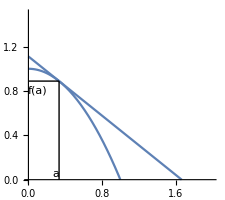

```mathematica
Remove["Global`*"]
```

y-y_0=k(x-x_0)
y=k(x-x_0)+y_0
y=f'(a)(x-a)+f(a)

```mathematica
f[x_]:=1-x^2
g[x_]:=f'[a](x-a)+f[a]
```

```mathematica
bas=x/.Solve[g[x]==0]//First
```

Triangelarea

```mathematica
Atri=1/2 g[0]bas
```

```mathematica
Plot[Atri,{a,0,1}]
```

```mathematica
Solve[D[Atri,a]==0.]//Last
```

```mathematica
g[x]
```

```mathematica
Manipulate[Plot[{f[x],-a^2-2 a (x-a)+1},{x,0,2},AspectRatio->Automatic,PlotRange->{{0,2},{0,2}}],{a,0,1}]
```

```mathematica
Plot[{f[x],-a^2-2 a (x-a)+1}/.a->1/3,{x,0,2},AspectRatio->Automatic,PlotRange->{{0,2},{0,3/2}},Ticks->None,Epilog->{Line[{{1/3,0},{1/3,f[1/3]}}],Line[{{0,f[1/3]},{1/3,f[1/3]}}],Text["a",{0.3,0.05}],Text["f(a)",{0.1,0.8}]}]
```